```mathematica
Quit
```

```mathematica
Get@FileNameJoin[{NotebookDirectory[],"SUGRABases_view.wl"}];
SetDirectory[NotebookDirectory[]];
Clear[LSTList];
<<"./LSTList.wl";
```

LSTList[T]: List of LST base for given T=T^H+1.
Examples: For T=5 (T^H=4), list is

```mathematica
LSTList[5]
```

{{1,3,1,3,1},{1,2,2,2,1},{1,2,3,1,2},{3,1,2,3,1},{3,1,3,1,3},{2,3,1,2,3},{1,2,{1,3},1},{2,{1,2},3,1},{2,{2,3},1,2},{3,1,{1,3},2},{2,{2,2},2,1},{2,2,{1,2},3},{2,{1,{1,3}},2},{1,{1,{1,4}},1},{2,1,{1,4},1},{3,{2,2},1,7},{2,1,4,1,2},{2,2,1,4,1},{2,2,2,1,4}}

## Supergravity base T<=193

#### Results

```mathematica
SUGRABases[T_,i_Integer]:=(Echo[LSTList[T][[i]],"LST base: "];
StateSummaryFromCompactDirectory[FileNameJoin@{NotebookDirectory[],"SUGRABase_Data"},T,i]//groupStateSummaryByTotalAdded)
SUGRABases[T_]:=StateSummaryFromCompactDirectory[FileNameJoin@{NotebookDirectory[],"SUGRABase_Data"},T]
```

This function generates Table of SUGRA bases where i-th base of LSTList[T]. 
In general, multiple tables are shown, corresponding to different number of external generator.

```mathematica
SUGRABases[2,1]
```

LST base:   {1,1}

<|1→,2→,3→Dataset[<>],4→Dataset[<>],5→Dataset[<>],6→Dataset[<>],7→Dataset[<>],8→|>

```mathematica
SUGRABases[41,1]
```

LST base:   {1,3,1,5,1,3,2,2,1,{1,12},1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,{1,12},1,2,2,2,2}

<|1→,2→,3→|>

```mathematica
SUGRABases[193,1]
```

LST base:   {1,2,2,3,1,5,1,3,2,2,1,{1,12},1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,12,1,2,2,3,1,5,1,3,2,2,1,{1,12},1,2,2,3,1,5,1,3,2,2,1}

<|2→|>

{{2,15899},{3,9243},{4,42216},{5,85904},{6,97608},{7,75399},{8,81633},{9,85049},{10,78802},{11,66930},{12,65595},{13,63165},{14,53942},{15,41971},{16,41082},{17,49007},{18,41979},{19,31620},{20,35348},{21,37989},{22,34768},{23,33431},{24,27430},{25,23396},{26,22909},{27,21308},{28,18785},{29,21309},{30,16377},{31,16063},{32,15872},{33,15145},{34,12131},{35,9910},{36,9303},{37,8438},{38,8299},{39,7017},{40,5896},{41,4638},{42,4936},{43,5230},{44,4734},{45,3563},{46,2695},{47,3276},{48,2913},{49,2953},{50,1695},{51,1639},{52,2366},{53,2568},{54,2013},{55,1583},{56,1389},{57,1310},{58,1498},{59,1208},{60,1068},{61,506},{62,642},{63,651},{64,829},{65,395},{66,190},{67,169},{68,183},{69,164},{70,188},{71,191},{72,135},{73,223},{74,207},{75,229},{76,93},{77,57},{78,38},{79,45},{80,73},{81,82},{82,70},{83,64},{84,107},{85,93},{86,118},{87,26},{88,26},{89,22},{90,17},{91,20},{92,51},{93,33},{94,42},{95,78},{96,69},{97,105},{98,13},{99,15},{100,42},{101,60},{102,8},{103,12},{104,33},{105,20},{106,36},{107,65},{108,62},{109,28},{110,28},{111,9},{112,37},{113,50},{114,1},{115,6},{116,30},{117,17},{118,35},{119,62},{120,17},{121,18},{122,28},{123,8},{124,34},{125,7},{126,0},{127,6},{128,28},{129,15},{130,32},{131,9},{132,5},{133,8},{134,3},{135,0},{136,1},{137,3},{138,0},{139,1},{140,1},{141,0},{142,0},{143,1},{144,2},{145,2},{146,1},{147,0},{148,0},{149,2},{150,0},{151,0},{152,0},{153,0},{154,0},{155,0},{156,1},{157,1},{158,0},{159,0},{160,0},{161,1},{162,0},{163,0},{164,0},{165,0},{166,0},{167,0},{168,0},{169,1},{170,0},{171,0},{172,0},{173,0},{174,0},{175,0},{176,0},{177,0},{178,0},{179,0},{180,0},{181,1},{182,0},{183,0},{184,0},{185,0},{186,0},{187,0},{188,0},{189,0},{190,0},{191,0},{192,0},{193,1}}

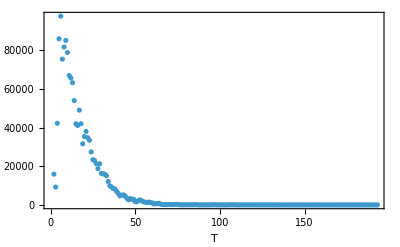

```mathematica
Table[{T,Length@SUGRABases[T]},{T,2,193}]
ListPlot[%,Frame->True,PlotRange->All,FrameLabel->{"T",""}]
```